```mathematica
SetDirectory[NotebookDirectory[]];
Re1=Import["./RedataT30mu320.dat"];
Im1=Import["./ImdataT30mu320.dat"];
omega=Table[i,{i,1,2001}];
spec=Transpose[{omega,-1/π*Im1[[75]]/(Re1[[75]]^2+Im1[[75]]^2)}];
intRe=Table[Interpolation[Transpose[{omega,Re1[[i]]}],InterpolationOrder->1],{i,1,201}];
intIm=Table[Interpolation[Transpose[{omega,Im1[[i]]}],InterpolationOrder->1],{i,1,201}];
specList=Table[With[{fIm=intIm[[i]],fRe=intRe[[i]]},-(1/π)*fIm[#]/(fRe[#]^2+fIm[#]^2)&],{i,1,201} ];
```

```mathematica
pole=Table[FindRoot[intRe[[i]][x],{x,√((i*10)^2+256.304^2)}][[1]][[2]]//Quiet,{i,1,201}];
Impole=Table[intIm[[i]][pole[[i]]],{i,1,201}]//Quiet;
rhopeak=Table[-1/π*Impole[[i]]/Impole[[i]]^2,{i,1,200}];
```

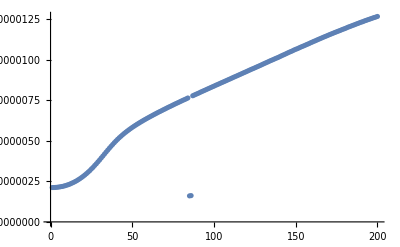

```mathematica
ListPlot[rhopeak]
```

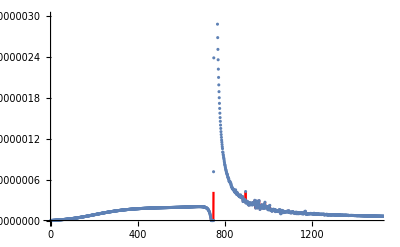

```mathematica
Show[Plot[specList[[75]][x],{x,1,2000},PlotPoints->30000,PlotStyle->Red],ListPlot[spec],PlotRange->{{0,1500},{-2 10^-8,3 10^-6}}]
```

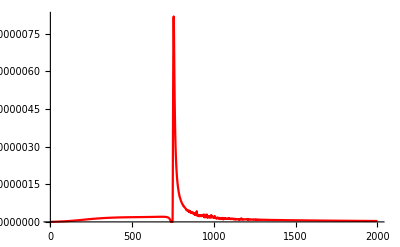

```mathematica
Plot[specList[[75]][x],{x,1,2000},PlotPoints->300,PlotStyle->Red,PlotRange->All]
```

```mathematica
specdata=Table[specList[[i]][x],{i,1,201},{x,1,2001,1}];
```

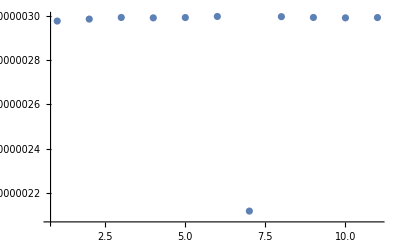

```mathematica
ListPlot[specdata[[1]][[190;;200]],PlotRange->All]
```

```mathematica
specdatapeakrep=Table[specdata[[i]][[Position[specdata[[i]],Max[specdata[[i]]]][[1]][[1]]]],{i,1,201}];
```

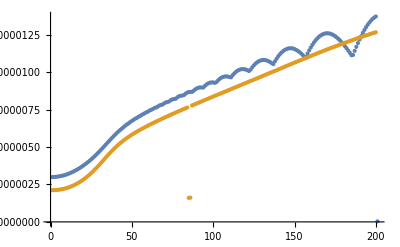

```mathematica
ListPlot[{specdatapeakrep,rhopeak}]
```

```mathematica
ListPlot3D[specdata(*,ScalingFunctions->Automatic*),PlotRange->{All,All,All(*{0,2 10^-6}*)}]
```

-Graphics3D-

```mathematica
specdata1=Table[{i,specdata[[j]][[i]]},{j,1,201},{i,1,2001}];
```

```mathematica
Length[specdata[[1]]]
```

2001

```mathematica
Dimensions[specdata1[[1]]]
```

{2001,2}

```mathematica
ListPlot3D[Re1]
```

-Graphics3D-

```mathematica
Table[Export["./T30mu320rhodata/rho_data_p"<>ToString[(i-1)*10]<>".dat",specdata1[[i]]],{i,1,201}];
```

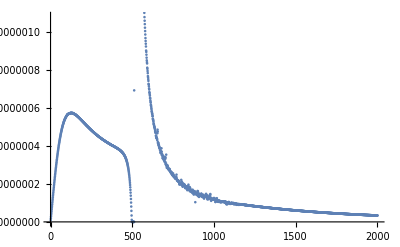

```mathematica
ListPlot[Import["./T30mu320rhodata/rho_data_p500.dat"]]
```